## Soma Calibration Theory

### Old, simple ρ_qua Calibration Theory

```mathematica
iinSimple[Iin_,Ilk_,pqua_]:=pqua Iin/Ilk
IinSimple[iin_,Ilk_,pqua_]:=(iin Ilk)/pqua
IlkSimple[iin_,Iin_,pqua_]:=(pqua Iin)/iin
```

#### Create the Evaluation Function that the distributions should be evaluated through

The Evaluation Function is the same as the firing rate equation (f=1/(τ·h(i_in))) except τ=ρ_tau/I_lk and h(i_in) is expanded out.

```mathematica
fireRSimple[Iin_,Ilk_,pqua_,ptau_]:=(Ilk √(2 pqua Iin/Ilk-1))/(ptau (π+2ArcCot[√(2 pqua Iin/Ilk-1)]))
```

As a test, plot the FI curve for an arbitrary I_lk, ρ_qua, and ρ_tau value.

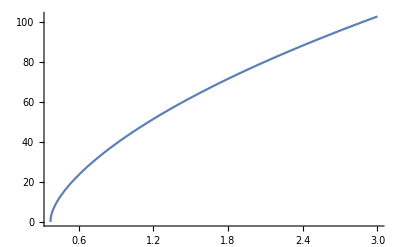

```mathematica
Plot[fireR[Iin,1.5,2,0.01,0.005],{Iin,0,3},PlotRange->{{0,All},{0,All}}]
```

#### Plot ρ_qua calibration curve as a function of I_lk

```mathematica
Manipulate[
Grid[{{
Show[
ContourPlot[{fireRSimple[Iin,Ilk,pqua,ptau]},{Iin,0,0.3},{Ilk,0.002,0.2},PlotRange->{0,Automatic},AxesLabel->{"I_in","I_lk"},ColorFunction->"SolarColors",PlotLegends->Automatic,ImageSize->Large],
Plot[{IlkSimple[1/2,Iin,pqua],IlkSimple[2,Iin,pqua]},{Iin,0,0.3},AxesLabel->{"I_lk","I_in"}]
]},{
Plot3D[{fireRSimple[Iin,Ilk,pqua,ptau]},{Iin,0,0.3},{Ilk,0.002,0.2},PlotRange->{0,All},Boxed->False,
ColorFunction->"SolarColors", ImageSize->Large,AxesLabel->{"I_in","I_lk","f"}
]
}}],
{{pqua,1.,"ρ_qua"},0.8,4,0.01,Appearance->"Open"},
{{ptau,0.0010,"ρ_tau"},0.0005,0.0020,0.0001,Appearance->"Open"}
]
```

#### Show how varying ρ_qua and ρ_ilkr change the bifurcation curve

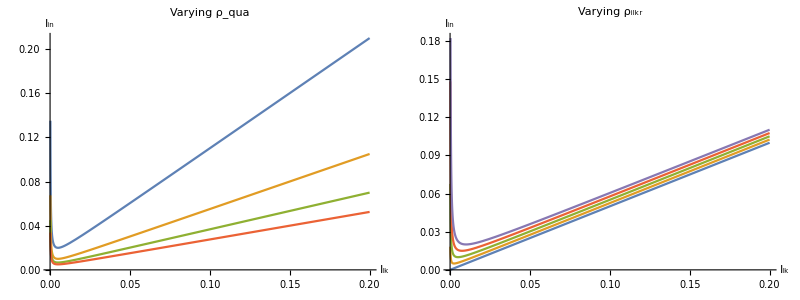

```mathematica
tmppqua=1.;
tmppilkr=0.005;
Grid[{{
Plot[{Iin[1/2,Ilk,tmppqua*0.5,tmppilkr],Iin[1/2,Ilk,tmppqua*1,tmppilkr],Iin[1/2,Ilk,tmppqua*1.5,tmppilkr],Iin[1/2,Ilk,tmppqua*2,tmppilkr]},
{Ilk,0.0002,0.2},
PlotLabel->"Varying ρ_qua",
AxesLabel->{"I_lk","I_in"},
ImageSize->Large]
,
Plot[{Iin[1/2,Ilk,tmppqua,tmppilkr*0.0],Iin[1/2,Ilk,tmppqua,tmppilkr*0.5],Iin[1/2,Ilk,tmppqua,tmppilkr*1.0],Iin[1/2,Ilk,tmppqua,tmppilkr*1.5],Iin[1/2,Ilk,tmppqua,tmppilkr*2.0]
},
{Ilk,0.0002,0.2},
PlotLabel->"Varying ρ_ilkr",
AxesLabel->{"I_lk","I_in"},
ImageSize->Large]
}
}]
```

### ρ_qua Calibration Theory

```mathematica
iin[Iin_,Ilk_,pqua_,pilkr_]:=pqua (Iin Ilk)/(Ilk+pilkr)^2
Iin[iin_,Ilk_,pqua_,pilkr_]:=(iin (Ilk + pilkr)^2)/(pqua Ilk)
```

#### Create the Evaluation Function that the distributions should be evaluated through

The Evaluation Function is the same as the firing rate equation (f=1/(τ·h(i_in))) except τ=ρ_tau/(I_lk+ρ_ilkr) and h(i_in) is expanded out.

```mathematica
fireR[Iin_,Ilk_,pqua_,ptau_,pilkr_]:=((Ilk+pilkr) √(2 pqua (Iin Ilk)/(Ilk+pilkr)^2-1))/(ptau (π+2ArcCot[√(2 pqua (Iin Ilk)/(Ilk+pilkr)^2-1)]))
```

As a test, plot the FI curve for an arbitrary I_lk, ρ_qua, and ρ_tau value.

```mathematica
Plot[fireR[Iin,1.5,2,0.01,0.005],{Iin,0,3},PlotRange->{{0,All},{0,All}}]
```

-Graphics-

#### Plot ρ_qua calibration curve as a function of I_lk

```mathematica
Manipulate[
Grid[{{
Show[
ContourPlot[{fireR[Iin,Ilk,pqua,ptau,pilkr]},{Ilk,0.002,0.2},{Iin,0,0.3},PlotRange->{0,Automatic},AxesLabel->{"ρ_qua","ρ_tau"},ColorFunction->"SolarColors",PlotLegends->Automatic,ImageSize->Large],
Plot[{Iin[1/2,Ilk,pqua,pilkr],Iin[2,Ilk,pqua,pilkr]},{Ilk,0.002,0.2},AxesLabel->{"I_lk","I_in"}]
]},{
Plot3D[{fireR[Iin,Ilk,pqua,ptau,pilkr],fireR[Iin,Ilk,pqua,ptau+.001,pilkr]},{Ilk,0.002,0.2},{Iin,0,0.3},PlotRange->{0,All},Boxed->False,
ColorFunction->"SolarColors", ImageSize->Large,AxesLabel->{"I_lk","I_in","f"}
]
}}],
{{pqua,1.,"ρ_qua"},0.8,4,0.01,Appearance->"Open"},
{{ptau,0.0010,"ρ_tau"},0.0005,0.0020,0.0001,Appearance->"Open"},
{{pilkr,0.005,"ρ_ilkr"},0.0000,.01,0.0001,Appearance->"Open"}
]
```

#### Show how varying ρ_qua and ρ_ilkr change the bifurcation curve

```mathematica
tmppqua=1.;
tmppilkr=0.005;
Grid[{{
Plot[{Iin[1/2,Ilk,tmppqua*0.5,tmppilkr],Iin[1/2,Ilk,tmppqua*1,tmppilkr],Iin[1/2,Ilk,tmppqua*1.5,tmppilkr],Iin[1/2,Ilk,tmppqua*2,tmppilkr]},
{Ilk,0.0002,0.2},
PlotLabel->"Varying ρ_qua",
AxesLabel->{"I_lk","I_in"},
ImageSize->Large]
,
Plot[{Iin[1/2,Ilk,tmppqua,tmppilkr*0.0],Iin[1/2,Ilk,tmppqua,tmppilkr*0.5],Iin[1/2,Ilk,tmppqua,tmppilkr*1.0],Iin[1/2,Ilk,tmppqua,tmppilkr*1.5],Iin[1/2,Ilk,tmppqua,tmppilkr*2.0]
},
{Ilk,0.0002,0.2},
PlotLabel->"Varying ρ_ilkr",
AxesLabel->{"I_lk","I_in"},
ImageSize->Large]
}
}]
```

-Graphics-

### Calibration parameter distribution analysis

This section is intended to show how having a distribution of ρ values in multiple dimensions extends or should extend to predicting the firing rate of a population of neurons.  In other words, should taking the median value of ρ_qua and ρ_tau and applying it to a population of neurons result in a firing rate distribution that has the median neuron going through the theoretical F-I curve?

#### Create Individual Distributions of ρ_qua and ρ_tau

Median of 𝒟 distribution: | 0.886538 | @ρ_qua= | 2.2

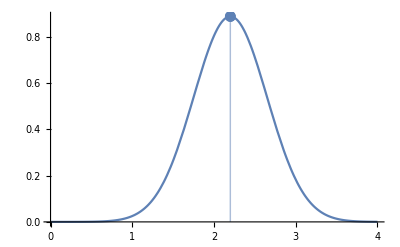

```mathematica
𝒟 =MixtureDistribution[{1,1},{NormalDistribution[1.25,0.20],NormalDistribution[2.0,0.3]}];
𝒟 =NormalDistribution[2.2,0.450];
Grid[{{Text["Median of 𝒟 distribution:"],PDF[𝒟,Median[𝒟]],Text["@ρ_qua="],Median[𝒟]}}]
Show[
Plot[PDF[𝒟,pqua],{pqua,0,4.0}],
ListPlot[{{Median[𝒟],PDF[𝒟,Median[𝒟]]}},Filling->Axis]
]
```

Median of ℰ distribution: | 1. | @ρ_tau= | 0.0011

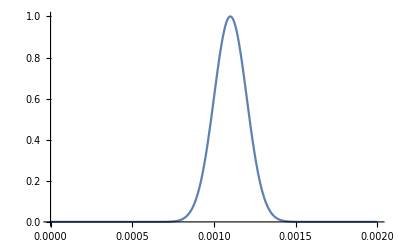

```mathematica
μ=.0011;
ℰ=NormalDistribution[μ,.0001];
Grid[{{Text["Median of ℰ distribution:"],PDF[ℰ,Median[ℰ]]/Max[PDF[ℰ,μ]],Text["@ρ_tau="],Median[ℰ]}}]
Plot[{PDF[ℰ,ptau]/Max[PDF[ℰ,μ]]},{ptau,0,.002},PlotRange->{0,All}]
```

#### Create the Joint Distribution of ρ_qua and ρ_tau

```mathematica
pquaRange={0,4.5};
ptauRange={0.00075,0.0015};
tmpIin = 1.0;
tmpIlk = 0.4;
pilkrVal = 0.0005;
```

```mathematica
𝒯𝒟=TransformedDistribution[{pqua,ptau},{pqua\[Distributed]𝒟,ptau\[Distributed]ℰ}];
(*PDF[𝒯𝒟,{pqua,ptau}]*)
```

```mathematica
Show[
Plot3D[{PDF[𝒯𝒟,{pqua,ptau}]},{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},{ptau,ptauRange⟦1⟧,ptauRange⟦2⟧},PlotRange->All,Boxed->False,ImageSize->Large,AxesLabel->{"ρ_qua","ρ_tau","#"},
RegionFunction->Function[{pqua,ptau},fireR[tmpIin,tmpIlk,pqua,ptau,pilkrVal]<fireR[tmpIin,tmpIlk,Median[𝒟],Median[ℰ],pilkrVal]],
ColorFunction->"DeepSeaColors"
],
Plot3D[{PDF[𝒯𝒟,{pqua,ptau}]},{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},{ptau,ptauRange⟦1⟧,ptauRange⟦2⟧},PlotRange->All,Boxed->False,ImageSize->Large,AxesLabel->{"ρ_qua","ρ_tau","#"},RegionFunction->Function[{pqua,ptau},fireR[tmpIin,tmpIlk,pqua,ptau,pilkrVal]>fireR[tmpIin,tmpIlk,Median[𝒟],Median[ℰ],pilkrVal]],
ColorFunction->"SolarColors"
],
ListPointPlot3D[{
{Median[𝒟],Median[ℰ],PDF[𝒯𝒟,{Median[𝒟],Median[ℰ]}]}
},
PlotStyle->Directive[Green,PointSize[Large]]]
]
```

-Graphics3D-

```mathematica
Grid[{
{
Text["Percentage of neurons under full joint distribution:"],
NIntegrate[If[PDF[𝒯𝒟,{pqua,ptau}]>0.01,PDF[𝒯𝒟,{pqua,ptau}],0],{pqua,0,5},{ptau,0,0.0025}, Method->"LocalAdaptive"]
},
{
Text["Percentage of neurons where f < f_median:"],
NIntegrate[If[fireR[tmpIin,tmpIlk,pqua,ptau,pilkrVal]<fireR[tmpIin,tmpIlk,Median[𝒟],Median[ℰ],pilkrVal],PDF[𝒯𝒟,{pqua,ptau}],0],{pqua,0,5},{ptau,0,0.0025},Method->"LocalAdaptive"]
},
{
Text["Percentage of neurons where f > f_median:"],
NIntegrate[If[fireR[tmpIin,tmpIlk,pqua,ptau,pilkrVal]>fireR[tmpIin,tmpIlk,Median[𝒟],Median[ℰ],pilkrVal],PDF[𝒯𝒟,{pqua,ptau}],0],{pqua,0,5},{ptau,0,0.0025},Method->"LocalAdaptive"]
}
}]
```

Percentage of neurons under full joint distribution: | 0.999997
Percentage of neurons where f < f_median: | 0.505693
Percentage of neurons where f > f_median: | 0.494306

#### Plot Firing Rate as a function of ρ_qua and ρ_tau

```mathematica
imgSz=450;
medFireColor =Blue;
Grid[{{
Manipulate[
Show[
ContourPlot[{fireR[Iin,Ilk,pqua,ptau,pilkrVal]},{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},{ptau,ptauRange⟦1⟧,ptauRange⟦2⟧},PlotRange->{0,fMax},AxesLabel->{"ρ_qua","ρ_tau"},ColorFunction->"SolarColors",ImageSize->imgSz,PlotLegends->Automatic],
Plot[ptau fireR[Iin,Ilk,pqua,ptau,pilkrVal]/fireR[Iin,Ilk,Median[𝒟],Median[ℰ],pilkrVal],{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},PlotStyle->Directive[Dashed,medFireColor]],
ListPlot[{{Median[𝒟],Median[ℰ]}},PlotStyle->Directive[medFireColor,PointSize[Medium]]]
]
,
{{Iin,1.5,"I_in"},0,10,0.1,Appearance-> "Open"},
{{Ilk,1.5,"I_lk"},0,10,0.1,Appearance-> "Open"},
{{fMax,1000,"f_max"},100,10000,10}
],
Manipulate[
Show[
Plot3D[fireR[Iin,Ilk,pqua,ptau,pilkrVal],{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},{ptau,ptauRange⟦1⟧,ptauRange⟦2⟧},PlotRange->{0,fMax},AxesLabel->{"ρ_qua","ρ_tau","f"},ColorFunction->"SolarColors",PlotLegends->Automatic,ImageSize->imgSz],
Plot3D[fireR[Iin,Ilk,Median[𝒟],Median[ℰ],pilkrVal],{pqua,pquaRange⟦1⟧,pquaRange⟦2⟧},{ptau,ptauRange⟦1⟧,ptauRange⟦2⟧},PlotStyle->Directive[Dashed,medFireColor]](*,
ListPlot[{{Median[𝒟],Median[ℰ]}},PlotStyle->Directive[Pink,PointSize[Medium]]]*)
],
{{Iin,1.5,"I_in"},0,10,0.1,Appearance-> "Open"},
{{Ilk,1.5,"I_lk"},0,10,0.1,Appearance-> "Open"},
{{fMax,1000,"f_max"},100,10000,10}]}}
]
```

```mathematica
{{, }}
```

### Methods that took too long to complete

```mathematica
Probability[fireR[1,1,pqua,ptau]<fireR[1,1,Median[𝒟],Median[ℰ]],{pqua\[Distributed]𝒟,ptau\[Distributed]ℰ}]
```

$Aborted

```mathematica
eval𝒯𝒟=TransformedDistribution[fireR[1,1,pqua,ptau],{pqua\[Distributed]𝒟,ptau\[Distributed]ℰ}];
Plot3D[{PDF[eval𝒯𝒟,{pqua,ptau}]},{pqua,0.5,4.0},{ptau,0,.002},PlotRange->All]
```

$Aborted